```mathematica
g=Monitor[Graph[Flatten[Table[Map[DirectedEdge[k,#[[1]],Framed[Magnify[#[[2]],.7], Background->LightGreen]]&,Connections[k]],{k,Sort[Keys[allGraphs5]]}]]],k];
```

```mathematica
g5=With[{good=Select[VertexList[g],VertexCount[allGraphs5[#,"graph"]]==5&]},Subgraph[g,Sort[good]]];
```

```mathematica
GraphDistanceMatrix[g5]//MatrixPlot
```

-Graphics-

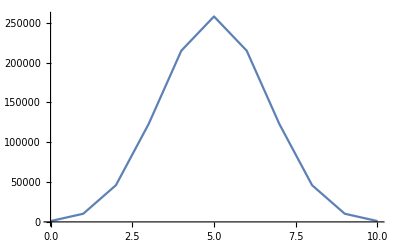

```mathematica
GraphDistanceMatrix[g5]//Flatten//Tally//ListLinePlot
```

```mathematica
((GraphDistanceMatrix[g5]//Flatten)//Tally)/1024
```

{{0,1},{1/1024,10},{1/512,45},{3/1024,120},{1/256,210},{5/1024,252},{3/512,210},{7/1024,120},{1/128,45},{9/1024,10},{5/512,1}}

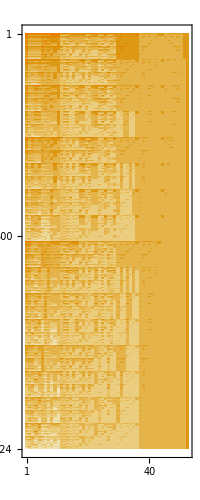

```mathematica
With[{base="C"},
MatrixPlot[
Table[GraphDistance[g,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]]
```

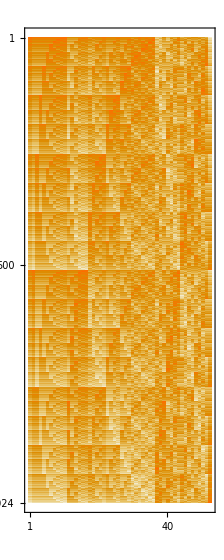

```mathematica
With[{base="G"},
MatrixPlot[
Table[GraphDistance[g5,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]]
```

```mathematica
With[{base="C"},
Map[Min,
Table[GraphDistance[g,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]//Tally//Sort]
```

{{0,1},{1,230},{2,712},{3,80},{4,1}}

```mathematica
With[{base="E"},
Map[Min,
Table[GraphDistance[g,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]//Tally//Sort]
```

{{0,1},{1,10},{2,55},{3,230},{4,728}}

```mathematica
With[{base="G"},
Map[Min,
Table[GraphDistance[g5,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]//Tally//Sort]
```

{{0,52},{1,300},{2,485},{3,177},{4,10}}

```mathematica
With[{base="F"},
Map[Min,
Table[GraphDistance[g5,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]//Tally//Sort]
```

{{0,52},{1,300},{2,485},{3,177},{4,10}}

```mathematica
With[{base="T"},
Map[Min,
Table[GraphDistance[g,key,b],{key,Sort[VertexList[g5]]},{b,Bases[base,"AtomKeys"]}]]//Tally//Sort]
```

{{0,1},{1,74},{2,758},{3,190},{4,1}}

```mathematica
Table[Labeled[Graph[EdgeList[allGraphs5[k,"graph"]],GraphLayout->"LayeredEmbedding", ImageSize->50, VertexLabels->"Name"],k],{k,Sort[Select[VertexList[g],VertexCount[allGraphs5[#,"graph"]]==5&&TreeGraphQ[allGraphs5[#,"graph"]]&]]}]
```

{-Graphics-760,-Graphics-766,-Graphics-768,-Graphics-814,-Graphics-820,-Graphics-822,-Graphics-840,-Graphics-846,-Graphics-976,-Graphics-982,-Graphics-984,-Graphics-1000,-Graphics-1008,-Graphics-1054,-Graphics-1056,-Graphics-1080,-Graphics-2218,-Graphics-2224,-Graphics-2226,-Graphics-2272,-Graphics-2278,-Graphics-2280,-Graphics-2298,-Graphics-2304,-Graphics-2434,-Graphics-2440,-Graphics-2442,-Graphics-2458,-Graphics-2466,-Graphics-2512,-Graphics-2514,-Graphics-2538,-Graphics-2946,-Graphics-2952,-Graphics-3000,-Graphics-3006,-Graphics-3162,-Graphics-3168,-Graphics-3186,-Graphics-3240,-Graphics-6592,-Graphics-6598,-Graphics-6600,-Graphics-6646,-Graphics-6652,-Graphics-6654,-Graphics-6672,-Graphics-6678,-Graphics-6808,-Graphics-6814,-Graphics-6816,-Graphics-6832,-Graphics-6840,-Graphics-6886,-Graphics-6888,-Graphics-6912,-Graphics-7318,-Graphics-7326,-Graphics-7372,-Graphics-7380,-Graphics-7398,-Graphics-7534,-Graphics-7542,-Graphics-7614,-Graphics-8776,-Graphics-8778,-Graphics-8830,-Graphics-8832,-Graphics-8856,-Graphics-8992,-Graphics-8994,-Graphics-9018,-Graphics-9504,-Graphics-9558,-Graphics-9720,-Graphics-19714,-Graphics-19720,-Graphics-19722,-Graphics-19768,-Graphics-19774,-Graphics-19776,-Graphics-19794,-Graphics-19800,-Graphics-19930,-Graphics-19936,-Graphics-19938,-Graphics-19954,-Graphics-19962,-Graphics-20008,-Graphics-20010,-Graphics-20034,-Graphics-20416,-Graphics-20422,-Graphics-20424,-Graphics-20496,-Graphics-20502,-Graphics-20656,-Graphics-20664,-Graphics-20736,-Graphics-21874,-Graphics-21880,-Graphics-21882,-Graphics-21900,-Graphics-21906,-Graphics-22114,-Graphics-22116,-Graphics-22140,-Graphics-22602,-Graphics-22608,-Graphics-22842,-Graphics-26248,-Graphics-26254,-Graphics-26256,-Graphics-26272,-Graphics-26280,-Graphics-26326,-Graphics-26328,-Graphics-26352,-Graphics-26974,-Graphics-26982,-Graphics-27054,-Graphics-28432,-Graphics-28434,-Graphics-28458,-Graphics-29160}

```mathematica
Table[Labeled[Graph[EdgeList[allGraphs5[k,"graph"]],GraphLayout->"LayeredEmbedding", ImageSize->{50,50}, VertexLabels->"Name"],k],{k,Sort[Bases["T","AtomKeys"]]}]
```

{-Graphics-19936,-Graphics-19940,-Graphics-19969,-Graphics-20029,-Graphics-20060,-Graphics-20721,-Graphics-20812,-Graphics-21420,-Graphics-21510,-Graphics-22287,-Graphics-22318,-Graphics-23072,-Graphics-23770,-Graphics-24384,-Graphics-24414,-Graphics-25168,-Graphics-25868,-Graphics-26821,-Graphics-26852,-Graphics-27610,-Graphics-28308,-Graphics-29128,-Graphics-29888,-Graphics-30586,-Graphics-31224,-Graphics-31984,-Graphics-32684,-Graphics-33130,-Graphics-33158,-Graphics-33916,-Graphics-34620,-Graphics-35434,-Graphics-36194,-Graphics-36898,-Graphics-37548,-Graphics-38308,-Graphics-39014,-Graphics-46180,-Graphics-46184,-Graphics-46942,-Graphics-47694,-Graphics-48460,-Graphics-49220,-Graphics-49972,-Graphics-50718,-Graphics-51478,-Graphics-52232,-Graphics-55252,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}